```mathematica
u[x_]=-Abs[x -1]*(1-Abs[x -1])/2
```

-1/2 (1-Abs[-1+x]) Abs[-1+x]

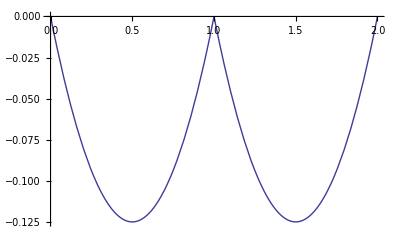

```mathematica
Plot[u[x],{x,0,2}]
```

```mathematica
uint[x_]=Assuming[{x>0,x<2},Integrate[u[t],{t,0,x}]]
```

Piecewise[{{1/12 (-6+12 x-9 x^2+2 x^3), 1<x<2}, {1/12 (-3 x^2+2 x^3), True}}]

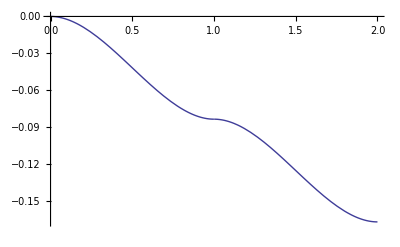

```mathematica
Plot[uint[x],{x,0,2}]
```

```mathematica
v[x_]=Assuming[{x>0,x<2},Simplify[(1/6)*(-2*u[x]- x*(2-x))]]
```

1/6 (-1+Abs[-1+x])

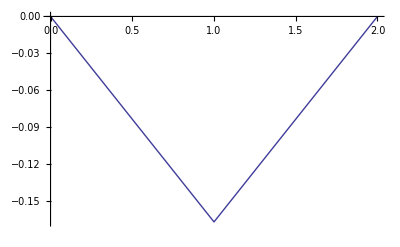

```mathematica
Plot[v[x],{x,0,2}]
```

```mathematica
vint[x_]=Assuming[{x>0,x<2},Integrate[v[t],{t,0,x}]]
```

Piecewise[{{-x^2/12, 0<x≤1}, {1/12 (2-4 x+x^2), True}}]

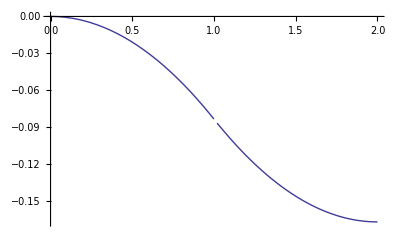

```mathematica
Plot[vint[x],{x,0,2}]
```

```mathematica
w[x_]=Simplify[u[x]-v[x]]
```

1/6 (1-4 Abs[-1+x]+3 Abs[-1+x]^2)

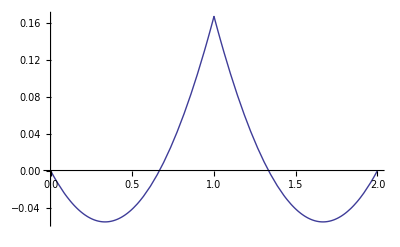

```mathematica
Plot[w[x],{x,0,2}]
```

```mathematica
wint[x_]=Assuming[{x>0,x<2},Integrate[w[t],{t,0,x}]]
```

Piecewise[{{1/6 (-4+8 x-5 x^2+x^3), 1<x<2}, {1/6 (-x^2+x^3), True}}]

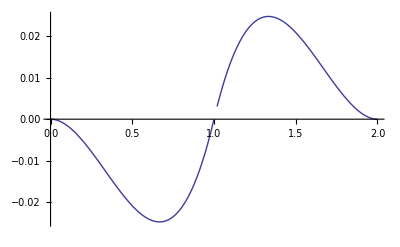

```mathematica
Plot[wint[x],{x,0,2}]
```

```mathematica
wintint[x_]=Assuming[{x>0,x<2},Integrate[wint[t],{t,0,x}]]
```

Piecewise[{{1/72 (16-48 x+48 x^2-20 x^3+3 x^4), 1<x<2}, {1/72 (-4 x^3+3 x^4), True}}]

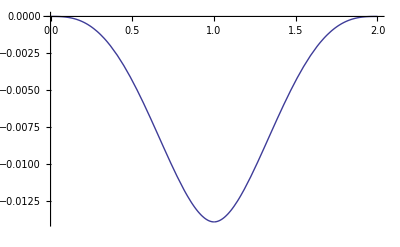

```mathematica
Plot[wintint[x],{x,0,2}]
```